```mathematica
x=1/c;
y=r*(c-1)/(c^2);
```

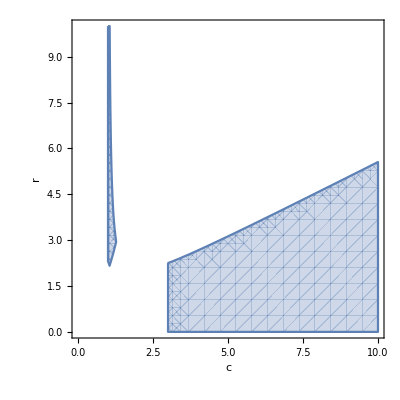

```mathematica
RegionPlot[{r*x*(1-x)+c*x*y<=1&&y+c*x*y<=1&&r>4*c/(3-c)&&0<x<1&&0<y<1},{c,0,10},{r,0,10},FrameLabel->{c,r}]
```

```mathematica
r=2.0004;
c=2.04;
```

```mathematica
x
```

0.490196

```mathematica
y
```

0.499908

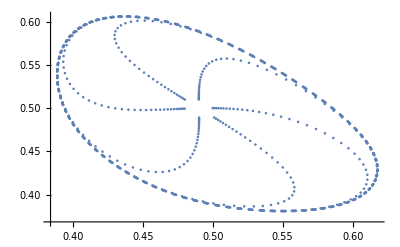

```mathematica
sol1=RecurrenceTable[{A[t+1]==(r+1)*A[t]-r*A[t]^2-c*A[t]*B[t],B[t+1]==c*A[t]*B[t],A[1]==0.5,B[1]==0.5},{A,B},{t,1000}];
ListPlot[sol1,PlotRange->All]
```

```mathematica
Clear[x]
```

```mathematica
Clear[c]
```

```mathematica
Clear[r]
```

```mathematica
Clear[y]
```

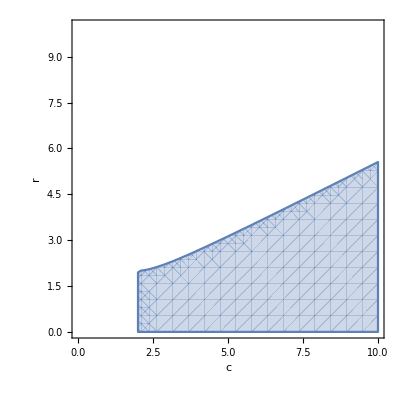

```mathematica
RegionPlot[{r*x*(1-x)+c*x*y<=1&&y+c*x*y<=1&&0<x<1&&0<y<1&&c>2},{c,0,10},{r,0,10},FrameLabel->{c,r}]
```

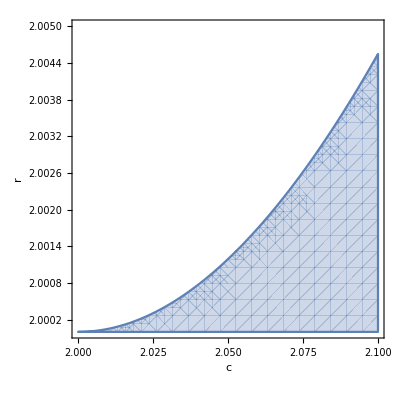

```mathematica
RegionPlot[{r*x*(1-x)+c*x*y<=1&&y+c*x*y<=1&&0<x<1&&0<y<1},{c,2,2.1},{r,2,2.005},FrameLabel->{c,r}]
```

```mathematica
r*0.7*(1-0.7)+c*0.7*0.7
```

1.41968